```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)
```

{surface0positive.gpl,surface1positive.gpl,surface2positive.gpl,surface3positive.gpl,surface4positive.gpl,surface5positive.gpl,surface6positive.gpl,surface7positive.gpl,surface8positive.gpl,surface9positive.gpl,surface10positive.gpl,surface11positive.gpl,surface12positive.gpl,surface13positive.gpl,surface14positive.gpl,surface15positive.gpl,surface16positive.gpl,surface17positive.gpl,surface18positive.gpl,surface19positive.gpl,surface20positive.gpl,surface21positive.gpl,surface22positive.gpl,surface23positive.gpl,surface24positive.gpl,surface25positive.gpl,surface26positive.gpl,surface27positive.gpl,surface28positive.gpl,surface29positive.gpl,surface30positive.gpl,surface31positive.gpl,surface32positive.gpl,surface33positive.gpl,surface34positive.gpl,surface35positive.gpl,surface36positive.gpl,surface37positive.gpl,surface38positive.gpl,surface39positive.gpl,surface40positive.gpl,surface41positive.gpl,surface42positive.gpl,surface43positive.gpl,surface44positive.gpl,surface45positive.gpl,surface46positive.gpl,surface47positive.gpl,surface48positive.gpl,surface49positive.gpl,surface50positive.gpl,surface51positive.gpl,surface52positive.gpl,surface53positive.gpl,surface54positive.gpl,surface55positive.gpl,surface56positive.gpl,surface57positive.gpl,surface58positive.gpl,surface59positive.gpl,surface60positive.gpl,surface61positive.gpl,surface62positive.gpl,surface63positive.gpl,surface64positive.gpl,surface65positive.gpl,surface66positive.gpl,surface67positive.gpl,surface68positive.gpl,surface69positive.gpl,surface70positive.gpl,surface71positive.gpl,surface72positive.gpl,surface73positive.gpl,surface74positive.gpl,surface75positive.gpl,surface76positive.gpl,surface77positive.gpl,surface78positive.gpl,surface79positive.gpl,surface80positive.gpl,surface81positive.gpl,surface82positive.gpl,surface83positive.gpl,surface84positive.gpl,surface85positive.gpl,surface86positive.gpl,surface87positive.gpl,surface88positive.gpl,surface89positive.gpl,surface90positive.gpl,surface91positive.gpl,surface92positive.gpl,surface93positive.gpl,surface94positive.gpl,surface95positive.gpl,surface96positive.gpl,surface97positive.gpl,surface98positive.gpl,surface99positive.gpl,surface100positive.gpl,surface101positive.gpl,surface102positive.gpl,surface103positive.gpl,surface104positive.gpl,surface105positive.gpl,surface106positive.gpl,surface107positive.gpl,surface108positive.gpl,surface109positive.gpl,surface110positive.gpl,surface111positive.gpl,surface112positive.gpl,surface113positive.gpl,surface114positive.gpl,surface115positive.gpl,surface116positive.gpl,surface117positive.gpl,surface118positive.gpl,surface119positive.gpl,surface120positive.gpl,surface121positive.gpl,surface122positive.gpl,surface123positive.gpl,surface124positive.gpl,surface125positive.gpl,surface126positive.gpl,surface127positive.gpl,surface128positive.gpl,surface129positive.gpl,surface130positive.gpl,surface131positive.gpl,surface132positive.gpl,surface133positive.gpl,surface134positive.gpl,surface135positive.gpl,surface136positive.gpl,surface137positive.gpl,surface138positive.gpl,surface139positive.gpl,surface140positive.gpl,surface141positive.gpl,surface142positive.gpl,surface143positive.gpl,surface144positive.gpl,surface145positive.gpl,surface146positive.gpl,surface147positive.gpl,surface148positive.gpl,surface149positive.gpl,surface150positive.gpl,surface151positive.gpl,surface152positive.gpl,surface153positive.gpl,surface154positive.gpl,surface155positive.gpl,surface156positive.gpl,surface157positive.gpl,surface158positive.gpl,surface159positive.gpl,surface160positive.gpl,surface161positive.gpl,surface162positive.gpl,surface163positive.gpl,surface164positive.gpl,surface165positive.gpl,surface166positive.gpl,surface167positive.gpl,surface168positive.gpl,surface169positive.gpl,surface170positive.gpl}

{{50,5.55809×10^7},{60,5.55201×10^7},{70,5.50447×10^7},{80,5.35349×10^7},{90,5.26945×10^7},{100,5.18155×10^7},{110,5.09873×10^7},{120,5.01877×10^7},{130,4.80903×10^7},{140,4.73947×10^7},{150,4.67422×10^7},{160,4.61217×10^7},{170,4.55415×10^7},{180,4.49901×10^7},{190,4.44758×10^7},{200,4.39949×10^7},{210,4.38427×10^7},{220,4.35965×10^7},{230,4.3186×10^7},{240,4.27862×10^7},{250,4.24027×10^7},{260,4.20415×10^7},{270,4.23837×10^7},{280,4.20498×10^7},{290,4.17305×10^7},{300,4.14242×10^7},{310,4.08297×10^7},{320,3.90597×10^7},{330,3.88021×10^7},{340,3.85516×10^7},{350,3.80476×10^7},{360,3.75939×10^7},{370,3.62883×10^7},{380,3.60824×10^7},{390,3.56053×10^7},{400,3.53921×10^7},{410,3.50576×10^7},{420,3.45886×10^7},{430,3.42533×10^7},{440,3.31137×10^7},{450,3.29438×10^7},{460,3.27796×10^7},{470,3.26158×10^7},{480,3.24596×10^7},{490,3.16791×10^7},{500,3.14475×10^7},{510,3.13186×10^7},{520,3.09748×10^7},{530,3.08531×10^7},{540,3.07358×10^7},{550,2.98071×10^7},{560,2.96898×10^7},{570,2.95752×10^7},{580,2.94629×10^7},{590,2.93543×10^7},{600,2.92853×10^7},{610,2.91802×10^7},{620,2.91387×10^7},{630,2.90326×10^7},{640,2.88122×10^7},{650,2.87145×10^7},{660,2.86491×10^7},{670,2.85899×10^7},{680,2.81437×10^7},{690,2.80602×10^7},{700,2.79794×10^7},{710,2.78082×10^7},{720,2.77333×10^7},{730,2.766×10^7},{740,2.75979×10^7},{750,2.66075×10^7},{760,2.65356×10^7},{770,2.62732×10^7},{780,2.62412×10^7},{790,2.61734×10^7},{800,2.61063×10^7},{810,2.59043×10^7},{820,2.58487×10^7},{830,2.57898×10^7},{840,2.57348×10^7},{850,2.56566×10^7},{860,2.55832×10^7},{870,2.55306×10^7},{880,2.5478×10^7},{890,2.54557×10^7},{900,2.5403×10^7},{910,2.5351×10^7},{920,2.52997×10^7},{930,2.52489×10^7},{940,2.51987×10^7},{950,2.5149×10^7},{960,2.50998×10^7},{970,2.50511×10^7},{980,2.50027×10^7},{990,2.49601×10^7},{1000,2.49129×10^7},{1010,2.4866×10^7},{1020,2.4915×10^7},{1030,2.48708×10^7},{1040,2.48267×10^7},{1050,2.47828×10^7},{1060,2.47391×10^7},{1070,2.46955×10^7},{1080,2.4652×10^7},{1090,2.46085×10^7},{1100,2.45651×10^7},{1110,2.45216×10^7},{1120,2.44543×10^7},{1130,2.44104×10^7},{1140,2.43622×10^7},{1150,2.43299×10^7},{1160,2.43059×10^7},{1170,2.42605×10^7},{1180,2.42153×10^7},{1190,2.41681×10^7},{1200,2.42633×10^7},{1210,2.42235×10^7},{1220,2.41819×10^7},{1230,2.41473×10^7},{1240,2.45137×10^7},{1250,2.44767×10^7},{1260,2.53068×10^7},{1270,2.52977×10^7},{1280,2.52598×10^7},{1290,2.52213×10^7},{1300,2.53413×10^7},{1310,2.53038×10^7},{1320,2.52646×10^7},{1330,2.55986×10^7},{1340,2.55902×10^7},{1350,2.58884×10^7},{1360,2.58575×10^7},{1370,2.58561×10^7},{1380,2.58223×10^7},{1390,2.56161×10^7},{1400,2.5574×10^7},{1410,2.55433×10^7},{1420,2.54994×10^7},{1430,2.54533×10^7},{1440,2.54052×10^7},{1450,2.53551×10^7},{1460,2.62642×10^7},{1470,2.62082×10^7},{1480,2.615×10^7},{1490,2.63682×10^7},{1500,2.63049×10^7},{1510,2.63414×10^7},{1520,2.63919×10^7},{1530,2.63147×10^7},{1540,2.62322×10^7},{1550,2.6147×10^7},{1560,2.60535×10^7},{1570,2.75948×10^7},{1580,2.82092×10^7},{1590,2.83318×10^7},{1600,2.8167×10^7},{1610,2.80723×10^7},{1620,2.71957×10^7},{1630,2.65192×10^7},{1640,2.81882×10^7},{1650,2.79805×10^7},{1660,2.82725×10^7},{1670,2.80856×10^7},{1680,2.79016×10^7},{1690,2.93533×10^7},{1700,2.8312×10^7},{1710,2.80586×10^7},{1720,2.77907×10^7},{1730,2.75076×10^7},{1740,2.66642×10^7},{1750,2.63432×10^7}}

{{50,555.809},{60,555.201},{70,550.447},{80,535.349},{90,526.945},{100,518.155},{110,509.873},{120,501.877},{130,480.903},{140,473.947},{150,467.422},{160,461.217},{170,455.415},{180,449.901},{190,444.758},{200,439.949},{210,438.427},{220,435.965},{230,431.86},{240,427.862},{250,424.027},{260,420.415},{270,423.837},{280,420.498},{290,417.305},{300,414.242},{310,408.297},{320,390.597},{330,388.021},{340,385.516},{350,380.476},{360,375.939},{370,362.883},{380,360.824},{390,356.053},{400,353.921},{410,350.576},{420,345.886},{430,342.533},{440,331.137},{450,329.438},{460,327.796},{470,326.158},{480,324.596},{490,316.791},{500,314.475},{510,313.186},{520,309.748},{530,308.531},{540,307.358},{550,298.071},{560,296.898},{570,295.752},{580,294.629},{590,293.543},{600,292.853},{610,291.802},{620,291.387},{630,290.326},{640,288.122},{650,287.145},{660,286.491},{670,285.899},{680,281.437},{690,280.602},{700,279.794},{710,278.082},{720,277.333},{730,276.6},{740,275.979},{750,266.075},{760,265.356},{770,262.732},{780,262.412},{790,261.734},{800,261.063},{810,259.043},{820,258.487},{830,257.898},{840,257.348},{850,256.566},{860,255.832},{870,255.306},{880,254.78},{890,254.557},{900,254.03},{910,253.51},{920,252.997},{930,252.489},{940,251.987},{950,251.49},{960,250.998},{970,250.511},{980,250.027},{990,249.601},{1000,249.129},{1010,248.66},{1020,249.15},{1030,248.708},{1040,248.267},{1050,247.828},{1060,247.391},{1070,246.955},{1080,246.52},{1090,246.085},{1100,245.651},{1110,245.216},{1120,244.543},{1130,244.104},{1140,243.622},{1150,243.299},{1160,243.059},{1170,242.605},{1180,242.153},{1190,241.681},{1200,242.633},{1210,242.235},{1220,241.819},{1230,241.473},{1240,245.137},{1250,244.767},{1260,253.068},{1270,252.977},{1280,252.598},{1290,252.213},{1300,253.413},{1310,253.038},{1320,252.646},{1330,255.986},{1340,255.902},{1350,258.884},{1360,258.575},{1370,258.561},{1380,258.223},{1390,256.161},{1400,255.74},{1410,255.433},{1420,254.994},{1430,254.533},{1440,254.052},{1450,253.551},{1460,262.642},{1470,262.082},{1480,261.5},{1490,263.682},{1500,263.049},{1510,263.414},{1520,263.919},{1530,263.147},{1540,262.322},{1550,261.47},{1560,260.535},{1570,275.948},{1580,282.092},{1590,283.318},{1600,281.67},{1610,280.723},{1620,271.957},{1630,265.192},{1640,281.882},{1650,279.805},{1660,282.725},{1670,280.856},{1680,279.016},{1690,293.533},{1700,283.12},{1710,280.586},{1720,277.907},{1730,275.076},{1740,266.642},{1750,263.432}}

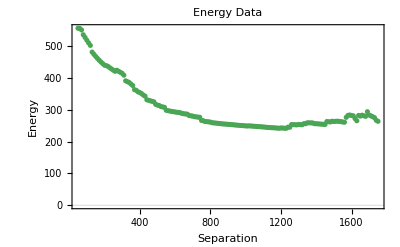

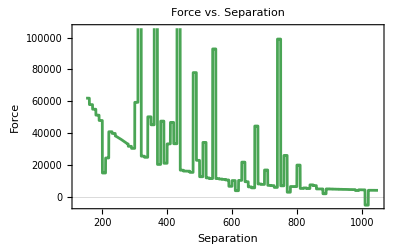

```mathematica
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues"];
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}]
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]]
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

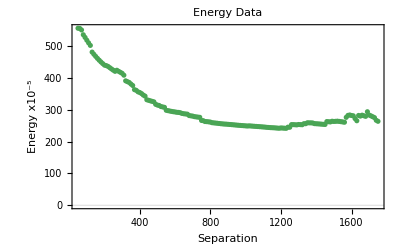

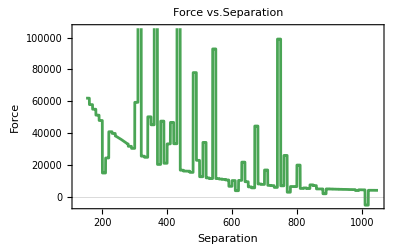

```mathematica
energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
```

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->20, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->{Automatic,Automatic,100}, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None];
prettyData
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{{-300,300},{-150,150},Automatic}];
Show[prettyData,Graphics3D[{Black,Sphere[{137.5,0,400},10],Cylinder[{{-137.5,0,399},{-137.5,0,401}},10]}]]
]
prettySurface["surface5positive.gpl"]
```

-Graphics3D-

```mathematica
|
```